```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
rplus = M+Sqrt[M^2-a^2];
tt=2 M r/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M r (r^2+a^2))/ρ)Sin[θ]^2;
tϕ=-4 a M r Sin[θ]^2/ρ;
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
```

```mathematica
a=.;M=.;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(r[τ]≤1.01*rplus),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
(* This one calculates u dot u *)
udotu[solni_,τval_]:=Block[{xα,uα},xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten; uα=D[xα,τ];
xα=xα/.τ->τval;uα=uα/.τ->τval;uα.((metric/.Table[coords[[i]]->xα[[i]],{i,1,n}]).uα)]
(* And this one prints out the coordinates *)
coordlist[τin_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

4000000

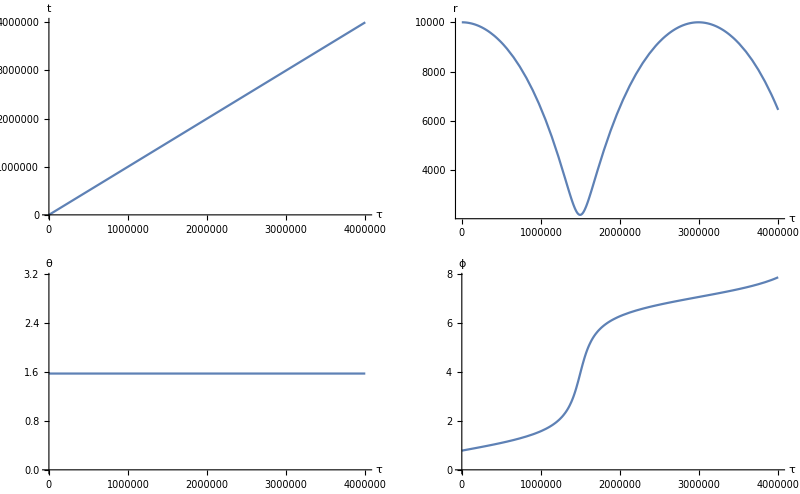

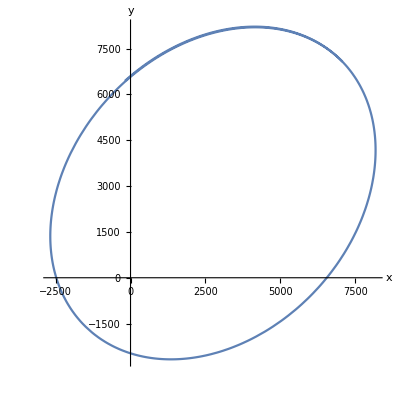

```mathematica
uinvar=-1; (* define u dot u to be -1 for massive particles *)
M=1;a=0.99 M;
maxτ=4000000;
(* check orbits very far away from the black hole *)
soln=computeSoln[maxτ,{0,0,0.0000006},{0,10000,π/2,Pi/4}];
τend
xyzsoln=sphslnToCartsln[soln];
GraphicsGrid[{{Plot[Evaluate[coords[[1]][τ]/.soln],{τ,0,τend},AxesLabel->{"τ","t"}],Plot[Evaluate[coords[[2]][τ]/.soln],{τ,0,τend},AxesLabel->{"τ","r"}]},{Plot[Evaluate[coords[[3]][τ]/.soln],{τ,0,τend},AxesLabel->{"τ","θ"}],Plot[Evaluate[coords[[4]][τ]/.soln],{τ,0,τend},AxesLabel->{"τ","ϕ"}]}}]
ParametricPlot[Evaluate[{xyzsoln[[1]],xyzsoln[[2]]}//Flatten],{τ,0,maxτ},AxesLabel->{x,y}]
```